```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
n=10; (* Points to sample along each connection *)
path=N@With[{Γ={0,0,0},X={0,1,0},W={1/2,1,0},L={1/2,1/2,1/2},kPts={3/4,3/4,0},U={1/4,1,1/4}},{L,kPts,U,W,Γ,X,W,L,Γ,kPts,U,X}]; (* The list of high-symmetry points *)
kPts=Subdivide[#1,#2,n]&@@@Partition[path,2,1]//Flatten[#,1]&//DeleteAdjacentDuplicates;(* List of n points sampled along each line of the path going through the high-symmetry points, it's literally the points generated by traversing the line, although not in equal steps *)
Length@kPts (* Total count of the sampling points *)
Graphics3D[{Point[#]&/@kPts,Line[path]},Axes->True]
```

111

-Graphics3D-

```mathematica
basis=N@{{1,-1,1},{1,1,-1},{-1,1,1}}; (* The basis for the G *)
G=Tuples[Range[-2,2],3].basis//Take[#,Length@kPts]&; (* All possible combinations that give the G points *)
Length@G (* Number of sampled points *)
(* 1BZ represented for a bcc lattice *)
With[{G=Tuples[Range[-1,1],3].basis},Show[VoronoiMesh[G,PlotTheme->"Lines",MeshCellStyle->{{3,"Interior"}->Directive[Opacity[0.8]]}],Graphics3D[{{AbsolutePointSize[7],Red,Point[G]},{Thick,Line[path]}}],PlotRange->Automatic]]
```

111

-Graphics3D-

```mathematica
allCombs=Tuples[{kPts,G,G}]//Partition[#,Length@G]&;
```

```mathematica
<<Notation`
```

```mathematica
Notation[Subscript[x_, n_] ⟺ x_[[n_]]]
```

```mathematica
d=N@{{0,0,0},{1/4,1/4,1/4}};
```

```mathematica
M=(1/2 Norm[#1+#2]^2+∑_(ν=1)^2 Exp[-I Dot[#2-#3,Subscript[d, ν]]])&@@@#&/@allCombs//Partition[#,Length@G]&;
```

```mathematica
λ=Eigenvalues[#]&/@M;
```

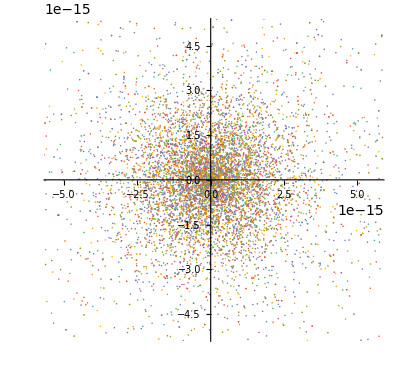

```mathematica
ComplexListPlot[λ,PlotRange->Automatic]
```